```mathematica
DrawIsoLines [debit_ , coordinates_,xminlim_,xmaxlim_,yminlim_,ymaxlim_,phiCount_,psiCount_] := Module [
{we= debit,
coords = coordinates,
xminl=xminlim,
xmaxl=xmaxlim,
yminl=yminlim,
ymaxl=ymaxlim,
phiC=phiCount,
psiC=psiCount,
phi,psi,w,g1,g2},
w[z_]=0;
For[i=1,i<=Length[we],i++,w[z_]=w[z]+we[[i]]/(2π)*Log[z-(coords[[i,1]]+I*coords[[i,2]])]];
phi[z_]=Re[w[z]];
psi[z_]=Im[w[z]];
g1=ContourPlot[phi[x+I*y],{x,xminl,xmaxl},{y,yminl,ymaxl},PlotLegends->Automatic, Contours->phiC,ContourShading->None,AspectRatio->Automatic];
g2=ContourPlot[psi[x+I*y],{x,xminl,xmaxl},{y,yminl,ymaxl},PlotLegends->Automatic, Contours->psiC,ContourShading->None,AspectRatio->Automatic];
Show[g1,g2]];
```

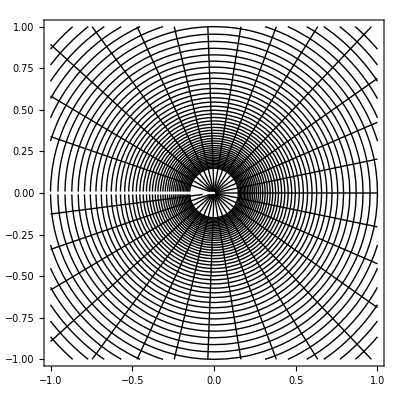

```mathematica
(*Первое задание*)
DrawIsoLines[{-1},{{0,0}},-1,1,-1,1,50,30]
```

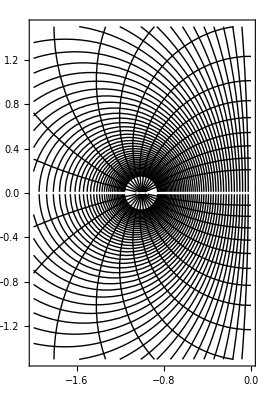

```mathematica
(*Второе задание*)
DrawIsoLines[{-1,1},{{-1,0},{1,0}},-2,0,-1.5,1.5,50,30]
```

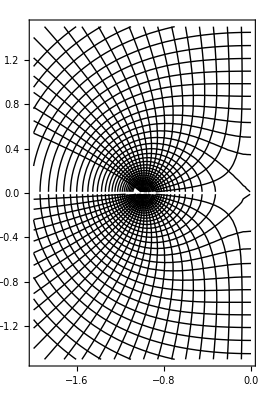

```mathematica
(*Третье задание*)
DrawIsoLines[{1,1},{{-1,0},{1,0}},-2,0,-1.5,1.5,30,100]
```

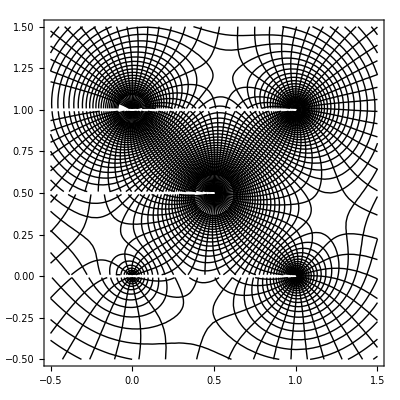

```mathematica
(*Четвертое задание*)
DrawIsoLines[{1,2,3,4,-5},{{0,0},{1,0},{1,1},{0,1},{0.5,0.5}},-0.5,1.5,-0.5,1.5,50,100]
```